# LQR Control of Double Pendulum

The double pendulum is a two link system that roughly approximates a two link quadruped leg when the leg is on the ground. This document shows a method to stabilize the leg to a fixed point by linearizing the dynamics of the leg around the operating point using Taylor Series and then implementing a Lnear Quadratic Regulator (LQR) to stabilize the system around that point. First the system is stabilized around the fixed point that is vertically up. Then stabiization around other fixed points are explored. Using this method the leg can be stabilized around a particular stance.

## Creating the controller

T[t] and V[t] represent the kinetic an potential energies of the system and L[t] is the Lagrangian. The EulerEquations[] function applies the Euler-Lagrange equations to L[t]. Then a NonLinearStateSpaceModel object is created which is a complete model of the pendulum. The dynamics of the pendulum are linearized around the desired operating point and and the LQR feedback gains of the controller are determined.

Now that the control system for stabilizing a stance has been implemented this work can be extended to locomotion. When a leg is on the ground (and no slipping is assumed) a leg on the ground behaves like an inverted double pendulum. One strategy for motion is to hold the leg steady using an LQR and when motion is required, destabilize the system so that it moves close to the target state and then stabilize around this new state. For example, take a one legged hopper. It behaves like a double pendulum when it is on the ground and stable. To make the leg hop from one position to another, destabilize the leg and launch it in a ballistic trajectory. Once the leg lands, use an LQR to stabilize the leg again. By doing this repeatedly, the leg can travel.

```mathematica
Needs["VariationalMethods`"];
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
pars={m1->1,m2->1,g->9.81,l1->1,l2->0.5};
T[t_]=1/2 m1 l1^2 θ1'[t]^2+1/2 m2(l1^2θ1'[t]^2+l2^2θ2'[t]^2+2 l1 l2 θ1'[t]θ2'[t] Cos[θ1[t]-θ2[t]]);
V[t_]= -(m1+m2)g l1 Cos[θ1[t]]-m2 g l2 Cos[θ2[t]];
L[t]=T[t]-V[t];
Expand[eqns={EulerEquations[L[t],θ1[t],t]/.{0->F[t]},EulerEquations[L[t],θ2[t],t]}];
dpend=NonlinearStateSpaceModel[eqns/.pars,{{θ1[t],180°},{θ2[t],180°}},{F[t]},{θ1[t],θ2[t]},t]
k=LQRegulatorGains[StateSpaceModel[dpend/.pars],{IdentityMatrix[4],{{1}}}];
csys= SystemsModelStateFeedbackConnect[dpend,k]
```

x_2[t](0.5 Cos[x_1[t]-x_3[t]] (0.+F[t]+19.62 Sin[x_3[t]]-0.5 Sin[x_1[t]-x_3[t]] x_2[t]^2))/(0.5-0.25 Cos[x_1[t]-x_3[t]]^2)-(2 (0.+4.905 Sin[x_1[t]]+0.5 Sin[x_1[t]-x_3[t]] x_4[t]^2))/(0.5-0.25 Cos[x_1[t]-x_3[t]]^2)x_4[t]-(0.25 (0.+F[t]+19.62 Sin[x_3[t]]-0.5 Sin[x_1[t]-x_3[t]] x_2[t]^2))/(0.5-0.25 Cos[x_1[t]-x_3[t]]^2)+(0.5 Cos[x_1[t]-x_3[t]] (0.+4.905 Sin[x_1[t]]+0.5 Sin[x_1[t]-x_3[t]] x_4[t]^2))/(0.5-0.25 Cos[x_1[t]-x_3[t]]^2)x_3[t]x_1[t]{x_1[t],180 °}x_2[t]{x_3[t],180 °}x_4[t] 4122NoneNoneFalseFalseFalse{F[t]}t

x_2[t](0.5 Cos[x_1[t]-x_3[t]] (0.+19.62 Sin[x_3[t]]+u_1[t]-98.5437 (-180 °+x_1[t])-19.9337 x_2[t]-0.5 Sin[x_1[t]-x_3[t]] x_2[t]^2-0.0254677 (-180 °+x_3[t])-19.8893 x_4[t]))/(0.5-0.25 Cos[x_1[t]-x_3[t]]^2)-(2 (0.+4.905 Sin[x_1[t]]+0.5 Sin[x_1[t]-x_3[t]] x_4[t]^2))/(0.5-0.25 Cos[x_1[t]-x_3[t]]^2)x_4[t]-(0.25 (0.+19.62 Sin[x_3[t]]+u_1[t]-98.5437 (-180 °+x_1[t])-19.9337 x_2[t]-0.5 Sin[x_1[t]-x_3[t]] x_2[t]^2-0.0254677 (-180 °+x_3[t])-19.8893 x_4[t]))/(0.5-0.25 Cos[x_1[t]-x_3[t]]^2)+(0.5 Cos[x_1[t]-x_3[t]] (0.+4.905 Sin[x_1[t]]+0.5 Sin[x_1[t]-x_3[t]] x_4[t]^2))/(0.5-0.25 Cos[x_1[t]-x_3[t]]^2)x_3[t]x_1[t]{x_1[t],180 °}x_2[t]{x_3[t],180 °}x_4[t] 4122NoneNoneFalseFalseFalse{u_1[t]}t

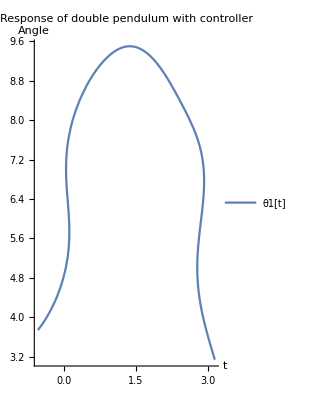

```mathematica
resp=OutputResponse[{dpend,{180°,0,179.999°,0}},0,{t,0,20}];
ParametricPlot[resp,{t,0,3},PlotLabel->"Response of double pendulum with controller",PlotLegends->{"θ1[t]","θ2[t]"},AxesLabel->{"t","Angle"}]
θ1s[t_]=resp[[1]];
θ2s[t_]=resp[[2]];
p1[t_]={l1 Sin[θ1s[t]],-l1 Cos[θ1s[t]]};
p2[t_]={l1 Sin[θ1s[t]]+l2 Sin[θ2s[t]],-l1 Cos[θ1s[t]]-l2 Cos[θ2s[t]]};
Table[p2[n],{n,0,0.1,0.01}];
Animate[Graphics[{Thick,Green,Line[{{0,0},p1[t],p2[t]}/.pars],Disk[p1[t]/.pars,0.1],Disk[p2[t]/.pars,0.1],Blue,BezierCurve[Table[p2[n]/.pars,{n,0,t,0.01}]]},PlotRange->{{-1.5,1.5},{-1.8,1.8}},Background->Lighter[Gray, 0.8]],{t,0,20},AnimationRunning->False,AnimationRate->1]
(*Export["dpend_sim2.gif",Table[Graphics[{Thick,Green,Line[{{0,0},p1[t],p2[t]}/.pars],Disk[p1[t]/.pars,0.1],Disk[p2[t]/.pars,0.1],Blue,BezierCurve[Table[p2[n]/.pars,{n,0,t,0.01}]]},PlotRange->{{-1.5,1.5},{-1.8,1.8}},Background->Lighter[Gray, 0.8]],{t,0,10,0.041667}],"FrameRate"->24]*)
```